# Boats Boats Boats Goats Boats

```mathematica
ClearAll[f]
```

2.

21000

{0.,0.914286}

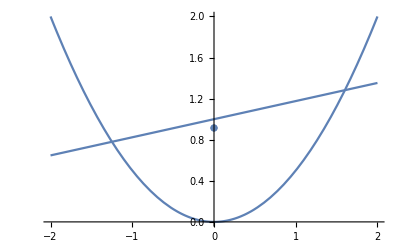

```mathematica
BoatCurve = Abs[x+0.15Sin[Abs[3x]]];
BoatCurve = 0.5x^2+0.1Sin[Abs[Pi*x]];
BoatCurve = x^2/2;

HeelAngle = 10;      (*degrees*)
BoatDensity = 300; (*kg/m^3*)
MassBalast = 5000 ;  (*kg*)
COBallast = {0,0};
BoatLength = 10;


xbd = x/.FindRoot[2-BoatCurve, {x, 2}]

mass = BoatLength*Integrate[BoatDensity,{x,y}∈boat]+MassBalast
disp = BoatLength*Integrate[1000,{x,y}∈under];
com = N[1/mass*(Integrate[BoatDensity*{x,y},{z, 0 ,10}, {x, -xbd, xbd},{y, BoatCurve, 2}]+MassBalast*COBallast)]

Show[Plot[BoatCurve, {x,-2,2}, PlotRange->{{-2,2},{0,2}}],Plot[Tan[HeelAngle Degree]*(x-0)+1, {x, -2,2}], ListPlot[{com}]]
com = Append[com, 0];
```

```mathematica
Torque[theta_]:=Module[{},
boat = ImplicitRegion[BoatCurve<y<2,{{x,-2,2},{y,-2,2}}];
water = ImplicitRegion[If[theta<90,y<Tan[theta Degree]*x+d,y>Tan[theta Degree]*x+d],{{x,-2,2},{y,-2,2}}];

under = RegionIntersection[boat,water];
disp = 1000*10*RegionMeasure[under];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = Append[RegionCentroid[under/.{d->draft}],0];
buoyancy = mass*98/10*{-Sin[theta Degree],Cos[theta Degree],0};
torque = Cross[cob-com,buoyancy][[3]];
torque
]
```

```mathematica
Torque[20]
```

56071.4

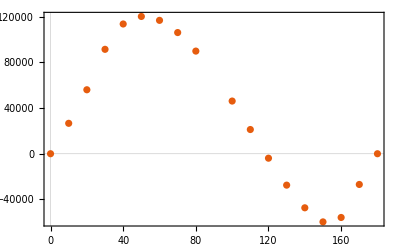

```mathematica
ListPlot[Table[{theta,Torque[theta]},{theta,{0,10,20,30,40,50,60,70,80,100,110,120,130,140,150,160,170,180}}], PlotTheme->"Scientific"]
```